# Homework Problem 2

-Graphics-

## a) Analytically determine the non-negative steady states (fixed points) of the model (2).

As to find a fixed point in a discrete system  needs to be fulfilled. The trivial case  = 0 can be located as the first FP. When solving the equation for a  so that the condition  is fulfilled .

```mathematica
ClearAll["Global`*"];

eq = N == (r + 1)*N/(1 + (N/K)^b);
(* Find a numerical solution for N *)
sol = NSolve[eq, N]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{N→0.},{N→1. (1000.^b r)^(1/b)}}

## b) Perform linear stability analysis and discuss how the linear stability of the non-negative steady states depends on the parameters

Lets take the derivative of the model in regard of N and check the “slope” at the found fixed points

```mathematica
ClearAll["Global`*"];
f1[n_] := (r + 1) * n / (1 + (n/K)^b)
f2[n_] = D[f1[n],n] // Simplify
```

(1000^b (1000^b-(-1+b) n^b) (1+r))/((1000^b+n^b)^2)

First we evaluate the FP N1* = 0.

```mathematica
f2[0] // Simplify
```

(1000^b (0^b+1000^b-0^b b) (1+r))/((0^b+1000^b)^2)

Further simplified one finds that the slope is .

Secondly  lets check the FP N2* =

```mathematica
f2[K*r^(1/b)] // Simplify
```

-((1+r) (-1-(r^(1/b))^b+b (r^(1/b))^b))/((1+(r^(1/b))^b)^2)

This  clears out to  , which describes the slope and therefore the stability.
Now to determine the stability we need to figure out it . In the first case the FP is unstable, in the second one stable.
For the FP1 N1* =  0, the slope of the linear approximation is , since  it follow that , we see that the system is unstable.
For the FP2 N2* = , the “eigenvalue” takes the form  . This means in terms of the stability that =1  is a critical point. As the term  can not become 0 (due to the constraints  and ), so the critical case is when  . As long as the term is smaller than 2 the FP is stable, if it is larger, the FP turns unstable.

We find a critical value for b, . In case of r = 0,  becomes 1. For values of the FP becomes stable, otherwise unstable.

## c) Analytically find all conditions on the parameters (within their ranges of validity) where a bifurcation from a stable steady state to an unstable steady state occurs.

As  described in subtask b), one finds a criticial depence of b in regard of r, . When b approaches  the stability of the FP changes.

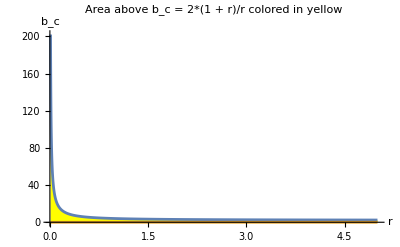

```mathematica
Plot[{2 * (1 + r)/r, 0}, {r, 0.01, 5}, 
 Filling -> {1 -> {2}}, 
 FillingStyle -> Yellow, 
 AxesLabel -> {"r", "b_c"}, 
 PlotRange -> All, 
 PlotLabel -> "Area above b_c = 2*(1 + r)/r colored in yellow"]
```

We  find  that when r goes to infinity . The stable combinations for the parameters lay in the yellow area in the plot.

## d) Investigate how the population size depends on time for the following values of the initial population size: N0 = 1, 2, 3 and 10. For each case, use the linear stability analysis performed in task b) to approximate the population dynamics in the vicinity of the unstable steady state. [Hint: treat the initial condition as a small perturbation around the unstable steady state, and plot how this perturbation, and consequently the population size, is expected to change over time according to the linear stability analysis.] Plot this approximation together with the corresponding (exact) population dynamics obtained by iterating Eq. (2). Use log-log scale for plotting to distinguish well between the different curves.

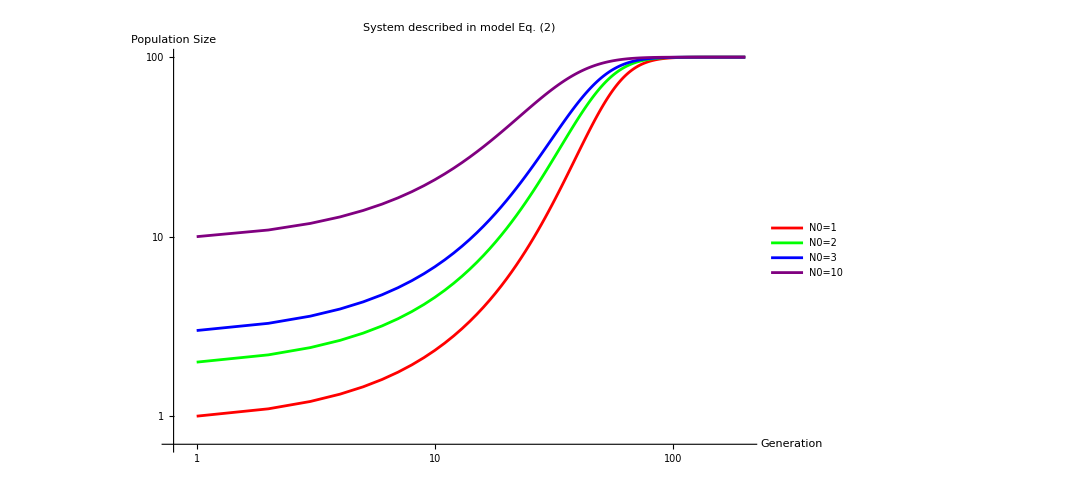

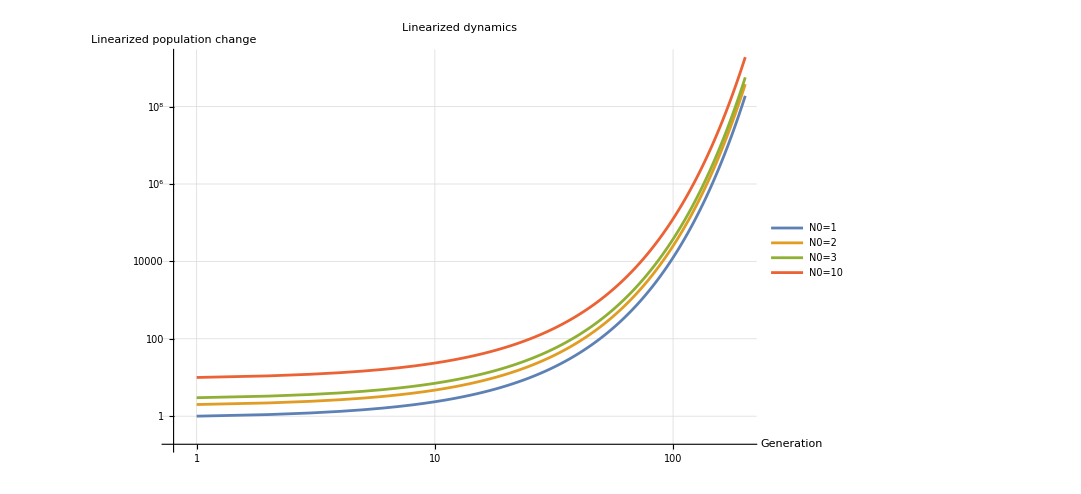

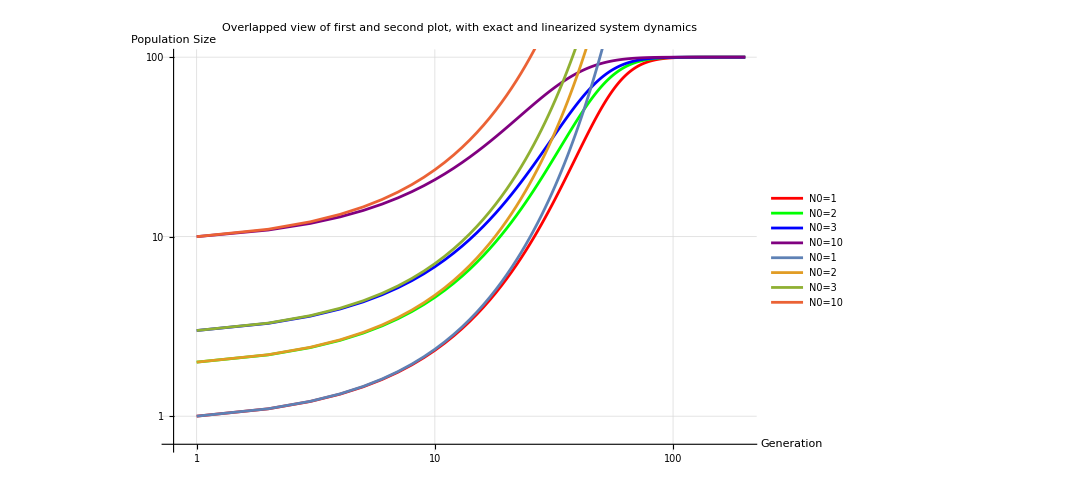

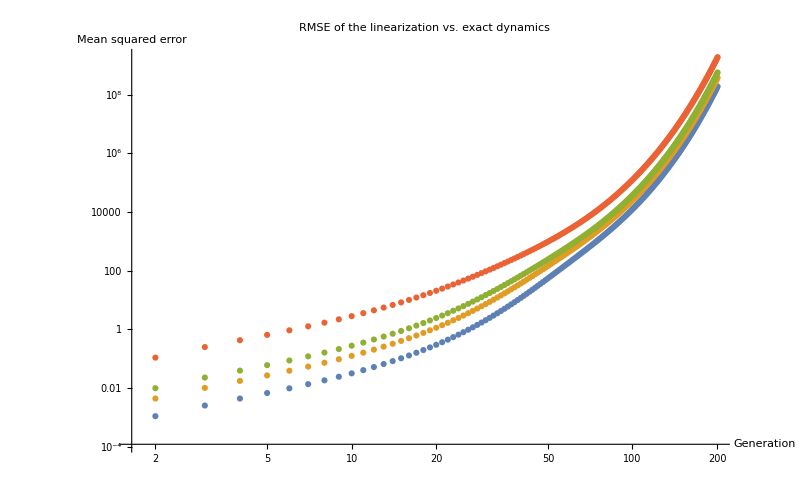

```mathematica
ClearAll["Global`*"];
K = 10^3;
r = 0.1;
b = 1;
N0values = {1,2,3,10};
unstableSteadyState = 0;
t0 = 0;
tMax = 200;

f2[n_] = n * (r+1) / (1 + (n/K)^b);
fPrime[n_] = Series[f2[n], {n, unstableSteadyState, 1}] // Normal ;
fLinear[n_] =  -((-1-(n/K)^b+b (n/K)^b) (1+r))/((1+(n/K)^b)^2);

(* Iteravile evaluate the function f2 for tMax generations with the four different starting values of N0*)

resultsSystem = Table[
   NestList[f2, unstableSteadyState + N0, tMax],
   {N0, N0values}
];
resultsSystem = resultsSystem;

resultsLinearized  = Table[
   NestList[fPrime, unstableSteadyState +N0, tMax],
   {N0, N0values}
];

(* Drop the 0 element of the linearized reults *) 
resultsLinearizedDropped = Map[Drop[#, 0] &, resultsLinearized];


Delta =  Sqrt[(resultsSystem - resultsLinearizedDropped) ^2]; 

 Plot1 = ListLogLogPlot[resultsSystem, PlotRange -> All, 
 PlotLegends -> {"N0=1", "N0=2", "N0=3", "N0=10"},
 Joined -> True,
 PlotLabel->"System described in model Eq. (2)",
 AxesLabel -> {"Generation", "Population Size"},
 GridLines->Automatic,
 PlotStyle -> {Red, Green, Blue, Purple},
 ImageSize -> {800, 600}]
 
 Plot2 =  ListLogLogPlot[resultsLinearizedDropped, PlotRange -> All, 
 PlotLegends -> {"N0=1", "N0=2", "N0=3", "N0=10"},
 Joined -> True,
 PlotLabel->"Linearized dynamics",
  AxesLabel -> {"Generation", "Linearized population change"},
  GridLines->Automatic,
  ImageSize -> {800, 600}]
 
 
 Show[Plot1, Plot2,
 PlotLabel -> "Overlapped view of first and second plot, with exact and linearized system dynamics",
 PlotStyle -> {Brown, Black, Yellow, Pink}
 ]
 
ListLogLogPlot[Delta,
   PlotRange -> {{Automatic, Automatic}, {Automatic, Automatic}},
   GridLines -> Automatic,
   PlotLabel -> "RMSE of the linearization vs. exact dynamics",
   ImageSize -> {800, 600},
   AxesLabel -> {"Generation", "Mean squared error"}
]
```

## e) Discuss how well the stability analysis approximates the exact dynamics. How does the initial condition influence the approximation?

As one would expect, small pertubations around an unstable fixed point do grow instead of shrink over time. Therefore our trajectories blow up over time. We see that in the early generations the approximation still holds quite well to the exact system, but then the trajectories blow up and diverge.

## f) Use linear stability analysis to approximate the dynamics in the vicinity of the stable steady state. Use initial population size N0 = N∗ +δN0, where N∗ is the value of the stable steady state and δN0 is an initial perturbation around N∗. Choose δN0 = −10, −3, −2, −1, 1, 2, 3 and 10. Proceed as follows. Starting from an initial perturbation δN0, approximate the dynamics until the system comes close to N∗ using the linear stability analysis around the stable steady state. Plot this approximation together with the exact dynamics, starting at N0. Perform the approximation for the different values of the initial perturbation δN0. How does the initial perturbation influence the approximation.

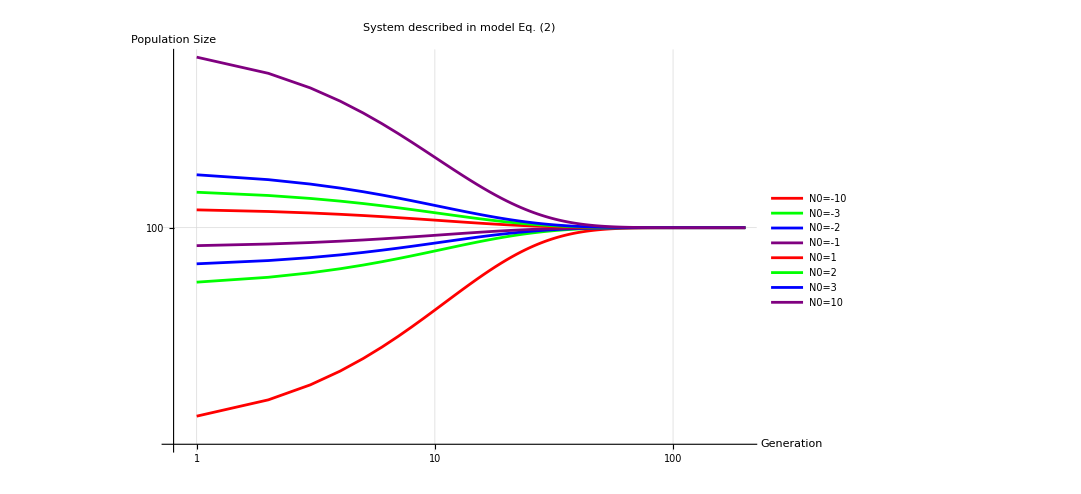

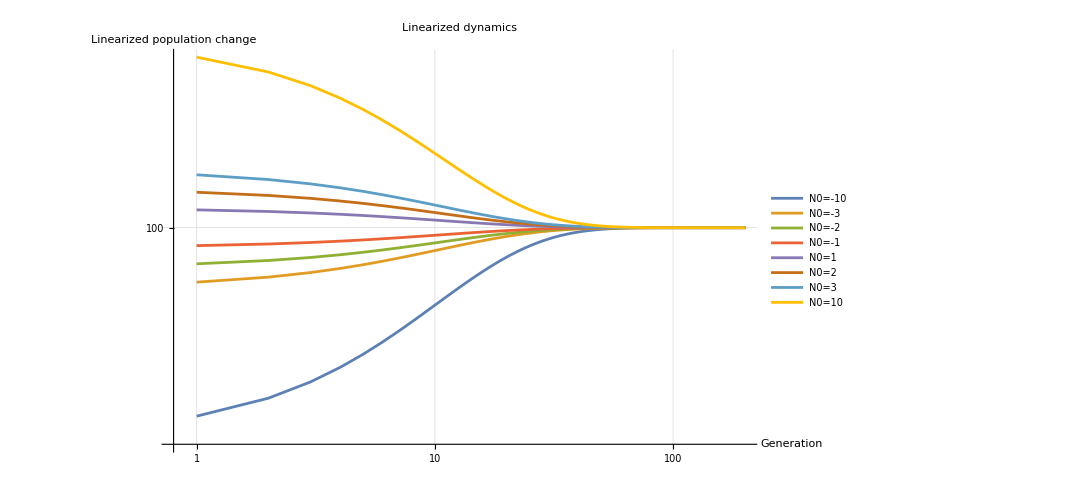

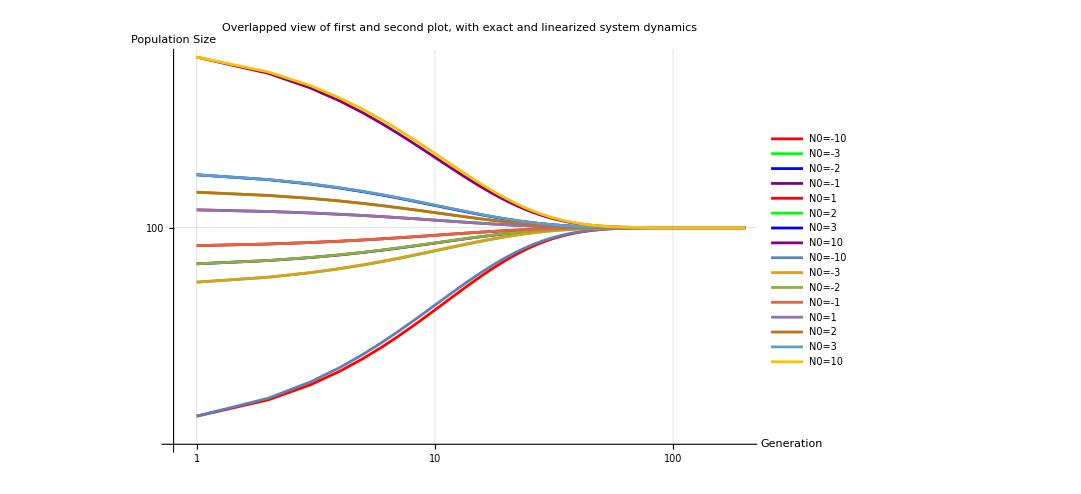

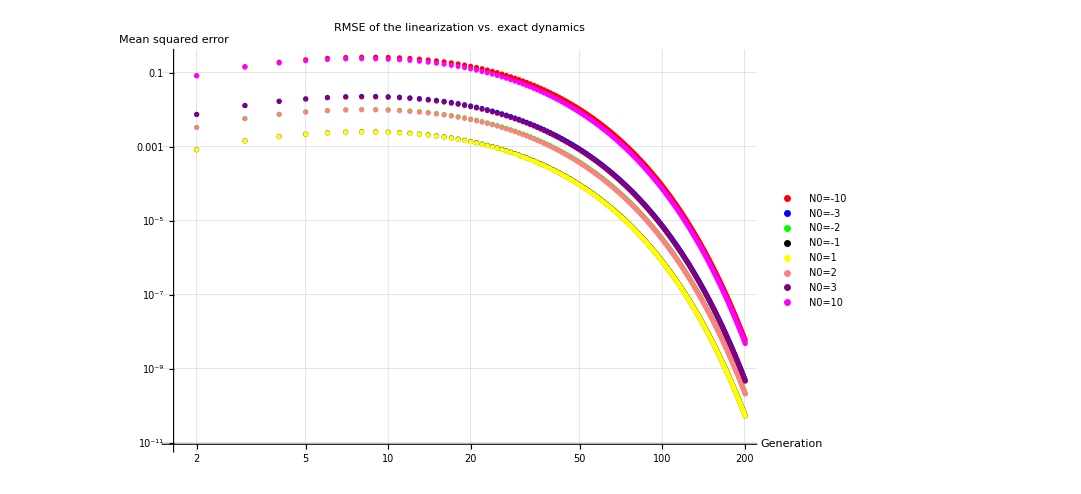

```mathematica
ClearAll["Global`*"];
K = 10^3;
r = 0.1;
b = 1;
N0values = {-10,-3, -2, -1, 1,2,3,10};
unstableSteadyState = 0;
evaluatedFP2 = K * r ^(1/b);
t0 = 0;
tMax = 200;

f2[n_] = n * (r+1) / (1 + (n/K)^b);
fPrime[n_] = Series[f2[n], {n, evaluatedFP2, 1}] // Normal ;
fLinear[n_] =  -((-1-(n/K)^b+b (n/K)^b) (1+r))/((1+(n/K)^b)^2);

(* Iteravile evaluate the function f2 for tMax generations with the four different starting values of N0*)

resultsSystem = Table[
   NestList[f2, evaluatedFP2 + N0, tMax],
   {N0, N0values}
];
resultsSystem = resultsSystem;

resultsLinearized  = Table[
   NestList[fPrime, evaluatedFP2 +N0, tMax],
   {N0, N0values}
];

(* Drop the 0 element of the linearized reults *) 
resultsLinearizedDropped = Map[Drop[#, 0] &, resultsLinearized];
Delta =  Sqrt[(resultsSystem - resultsLinearizedDropped) ^2];

legends = "N0=" <> ToString[#] & /@ N0values;

 Plot1 = ListLogLogPlot[resultsSystem, PlotRange -> All, 
 PlotLegends -> legends,
 Joined -> True,
 PlotLabel->"System described in model Eq. (2)",
 AxesLabel -> {"Generation", "Population Size"},
 GridLines->Automatic,
 PlotStyle -> {Red, Green, Blue, Purple},
 ImageSize -> {800, 600}]
 
 Plot2 =  ListLogLogPlot[resultsLinearizedDropped, PlotRange -> All, 
 PlotLegends -> legends,
 Joined -> True,
 PlotLabel->"Linearized dynamics",
  AxesLabel -> {"Generation", "Linearized population change"},
  GridLines->Automatic,
  ImageSize -> {800, 600}]
 
 
 Show[Plot1, Plot2,
 PlotLabel -> "Overlapped view of first and second plot, with exact and linearized system dynamics",
 PlotStyle -> {Brown, Black, Yellow, Pink}
 ]
 
ListLogLogPlot[Delta,
   PlotLegends -> legends,
   PlotRange -> {{Automatic, Automatic}, {Automatic, Automatic}},
   GridLines -> Automatic,
   PlotLabel -> "RMSE of the linearization vs. exact dynamics",
   ImageSize -> {800, 600},
   AxesLabel -> {"Generation", "Mean squared error"},
   PlotStyle-> {Red, Blue, Green, Black, Yellow, Pink, Purple, Magenta}
]
```

Oppositely to the approximation around the unstable FP, when linearizing around the stable FP we find that the perturbations shrink over time and get obviously “attracted”. We also find that the smaller the amplitude of the initial perturbation the smaller the approximation error.